```mathematica
<< xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M,4,IndexRange[a,q]];
DefChart[ch,M,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor -> Blue];
DefConstantSymbol[mass, PrintAs-> "M"];
DefConstantSymbol[aa,PrintAs-> "a"];
DefScalarFunction[rhob,PrintAs-> "ρb"];
DefScalarFunction[rhobc,PrintAs-> "ρbc"];
DefScalarFunction[rho,PrintAs-> "ρ"];
DefScalarFunction[del,PrintAs->"Δ"];
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefChart: Defining chart ch.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping ch.

** DefMapping: Defining inverse mapping ich.

** DefTensor: Defining mapping differential tensor dich[-a,icha].

** DefTensor: Defining mapping differential tensor dch[-a,cha].

** DefBasis: Defining basis ch. Coordinated basis.

** DefCovD: Defining parallel derivative PDch[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDch[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDch[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpch[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownch[-a,-b,-c,-d].

** DefConstantSymbol: Defining constant symbol mass.

** DefConstantSymbol: Defining constant symbol aa.

** DefScalarFunction: Defining scalar function rhob.

** DefScalarFunction: Defining scalar function rhobc.

** DefScalarFunction: Defining scalar function rho.

** DefScalarFunction: Defining scalar function del.

```mathematica
$Assumptions = mass >0 && r[] > 2 mass && 0 < θ[]<π && 0< ϕ[]< 2π && t[]∈Reals && aa∈Reals && rho[r[],θ[]]∈Reals &&del[r[]]∈Reals ; 
gg=CTensor[{{-(1- 2mass r[]/(rho[r[],θ[]])),0,0,-2aa mass r[]Sin[θ[]]^2/(rho[r[],θ[]])},{0,rho[r[],θ[]]/del[r[]],0,0},{0,0,rho[r[],θ[]],0},{-2aa mass r[]Sin[θ[]]^2/(rho[r[],θ[]]),0,0,(r[]^2+aa^2+(2aa^2mass r[]Sin[θ[]]^2/rho[r[],θ[]])) Sin[θ[]]^2}},{-ch,-ch}]/.del[r[]]->r[]^2+aa^2-2mass r[]/.rho[r[],θ[]]->r[]^2+aa^2Cos[θ[]]^2;
SetCMetric[gg,ch,SignatureOfMetric->{3,1,0}];
cd=CovDOfMetric[gg];

gmatrix= ComponentArray[gg[{-a,-ch},{-b,-ch}]] // MatrixForm;
```

```mathematica
weyl=Weyl[cd][{-a,-ch},{-b,-ch},{-c,-ch},{-d,-ch}];
```

```mathematica
(*La base tetrada*)
(*La base tetrada*)
l=CTensor[{(r[]^2+aa^2)/del[r[]],1,0,aa/del[r[]]},{ch}]/.del[r[]]->r[]^2+aa^2-2mass r[]/.rho[r[],θ[]]->r[]^2+aa^2Cos[θ[]]^2;
n=CTensor[1/(2rho[r[],θ[]]){r[]^2+aa^2,-del[r[]],0,aa},{ch}]/.del[r[]]->r[]^2+aa^2-2mass r[]/.rho[r[],θ[]]->r[]^2+aa^2Cos[θ[]]^2;
m=CTensor[1/(Sqrt[2](r[]+I aa Cos[θ[]])){I aa Sin[θ[]],0,1,I Csc[θ[]]},{ch}];
mb=CTensor[1/(Sqrt[2](r[]-I aa Cos[θ[]])){-I aa Sin[θ[]],0,1,-I Csc[θ[]]},{ch}];
```

```mathematica
n[a]m[-a]//Simplify
```

0

```mathematica
(*Se define el Killing*)
k=CTensor[{1,0,0,0},{ch}];

F= cd[-b]@k[-a]//Simplify;
F=Head[F];
Fd= F[-a,-b]+I/2 epsilon[gg][-a,-b,e,f]F[-e,-f];
Fd= Head[Fd];
```

```mathematica
σ= 2Fd[-a,-b]k[b]//Simplify;
σ=Head[σ];
```

```mathematica
DefScalarFunction[sg];
```

** DefScalarFunction: Defining scalar function sg.

```mathematica
cd[-a]@sg[r[],θ[]]==σ[-a] //Simplify
```

e |   | 2
a |   sg^(0,1)[r,θ]+e |   | 1
a |   sg^(1,0)[r,θ]==0
-(2 M)/(a Cos[θ]-ⅈ r)^2
(2 ⅈ a M Sin[θ])/(a Cos[θ]-ⅈ r)^2
0 |  
a

```mathematica
del[r[]]:=r[]^2+aa^2-2mass r[];
rho[r[],θ[]]:=Sqrt[r[]^2+aa^2*Cos[θ[]]^2];
rhob[r[],θ[]]:= r[]+I aa Cos[θ[]];
rhobc[r[],θ[]]:= r[]-I aa Cos[θ[]];
```

```mathematica
DSolve[Derivative[1,0][sg][r[],θ[]]==-(2 M)/(a Cos[θ[]]-ⅈ r[])^2,{sg[r[],θ[]]},{r[],θ[]}]
DSolve[Derivative[0,1][sg][r[],θ[]]==(2 ⅈ a M Sin[θ[]])/(a Cos[θ[]]-ⅈ r[])^2,{sg[r[],θ[]]},{r[],θ[]}]
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{{sg[r,θ]→C[1][θ]+-(2 M)/(a Cos[θ]-ⅈ K[1])^2K[1]1r}}

Attributes::notfound: Symbol DSolveDispatchODE not found.

{{sg[r,θ]→(2 ⅈ M)/(a Cos[θ]-ⅈ r)+C[1][r]}}

```mathematica
σE= 1-1+2mass/(r[]-I aa Cos[θ[]]) ;
```

```mathematica
(*Componentes del tensor de Weyl*)
ps0= -Weyl[cd][-a,-b,-c,-d]l[a]m[b]l[c]m[d]// Simplify;
ps1= -Weyl[cd][-a,-b,-c,-d]l[a]n[b]l[c]m[d]// Simplify;
ps2= 1/2 Weyl[cd][-a,-b,-c,-d](l[a]n[b]l[c]n[d]+l[a]n[b]m[c]mb[d])// Simplify;
ps3= Weyl[cd][-a,-b,-c,-d]l[a]n[b]n[c]mb[d]// Simplify;
ps4= -Weyl[cd][-a,-b,-c,-d]n[a]mb[b]n[c]mb[d]// Simplify;
```

```mathematica
0
```

0

```mathematica
ps2
```

-(ⅈ M)/(a Cos[θ]-ⅈ r)^3

```mathematica
(*Definos las matrices alpha*)
α1=m[-a]mb[-b]-mb[-a]m[-b]+l[-a]n[-b]-n[-a]l[-b] // Simplify;
α2= -l[-a] mb[-b]+mb[-a] l[-b]+m[-a] n[-b]-n[-a] m[-b] // Simplify;
α3= I(l[-a] mb[-b]-mb[-a] l[-b]+m[-a] n[-b]-n[-a] m[-b])// Simplify;
```

```mathematica
DefManifold[S3,3,{P,Q,S,R,T}];
DefChart[ch3,S3,{0,1,2},{u[],v[],w[]},ChartColor -> Red];


(*Métrica δ_ij=identidad 3x3*)
g3=CTensor[{{1,0,0},{0,1,0},{0,0,1}},{-ch3,-ch3}];
SetCMetric[g3,ch3,SignatureOfMetric->{0,3,0}];
cd3=CovDOfMetric[g3];

g3matrix= ComponentArray[g3[{-P,-ch3},{-Q,-ch3}]] // MatrixForm;
```

** DefManifold: Defining manifold S3.

** DefVBundle: Defining vbundle TangentS3.

** DefChart: Defining chart ch3.

** DefTensor: Defining coordinate scalar u[].

** DefTensor: Defining coordinate scalar v[].

** DefTensor: Defining coordinate scalar w[].

** DefMapping: Defining mapping ch3.

** DefMapping: Defining inverse mapping ich3.

** DefTensor: Defining mapping differential tensor dich3[-e,ich3P].

** DefTensor: Defining mapping differential tensor dch3[-P,ch3e].

** DefBasis: Defining basis ch3. Coordinated basis.

** DefCovD: Defining parallel derivative PDch3[-P].

** DefTensor: Defining vanishing torsion tensor TorsionPDch3[P,-Q,-R].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch3[P,-Q,-R].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch3[-P,-Q,-R,S].

** DefTensor: Defining vanishing Ricci tensor RicciPDch3[-P,-Q].

** DefTensor: Defining antisymmetric +1 density etaUpch3[P,Q,R].

** DefTensor: Defining antisymmetric -1 density etaDownch3[-P,-Q,-R].

```mathematica
Head[α3]//FullSimplify
```

CTensor[{{0,(ⅈ a (a^2 (2+Cos[2 θ])-2 (M+2 ⅈ a Cos[θ]) r-r^2) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r))),(a^2 (2+Cos[2 θ])-2 (M+2 ⅈ a Cos[θ]) r-r^2)/(2 √2 (a Cos[θ]-ⅈ r)),-(ⅈ √2 (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r) Sin[θ])/(4 a Cos[θ]-4 ⅈ r)},{-(ⅈ a (a^2+2 a^2 Cos[θ]^2-4 ⅈ a Cos[θ] r-r (2 M+r)) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r))),0,-((a Cos[θ]+ⅈ r) (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r))/(2 √2 (a^2+r (-2 M+r))),(ⅈ (a^2 (2+Cos[2 θ])-2 (M+2 ⅈ a Cos[θ]) r-r^2) (a^2+r^2) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r)))},{(-a^2 (2+Cos[2 θ])+2 (M+2 ⅈ a Cos[θ]) r+r^2)/(2 √2 (a Cos[θ]-ⅈ r)),((a Cos[θ]+ⅈ r) (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r))/(2 √2 (a^2+r (-2 M+r))),0,(a (a^2 (2+Cos[2 θ])-2 (M+2 ⅈ a Cos[θ]) r-r^2) Sin[θ]^2)/(2 √2 (a Cos[θ]-ⅈ r))},{(ⅈ (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r)),-(ⅈ (a^2+r^2) (a^2+2 a^2 Cos[θ]^2-4 ⅈ a Cos[θ] r-r (2 M+r)) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r))),(a (-a^2 (2+Cos[2 θ])+2 (M+2 ⅈ a Cos[θ]) r+r^2) Sin[θ]^2)/(2 √2 (a Cos[θ]-ⅈ r)),0}},{-ch,-ch},0]

```mathematica
(*Se crea ya si con los índices internos IJ en la subvariedad*)
Alpha=CTensor[{{{0,1,-ⅈ a Sin[θ],0},{-1,0,0,a Sin[θ]^2},{ⅈ a Sin[θ],0,0,-ⅈ (a^2+r^2) Sin[θ]},{0,-a Sin[θ]^2,ⅈ (a^2+r^2) Sin[θ],0}},{{0,-(a (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r))),(√2 (ⅈ a^2 Cos[2 θ]+(2 ⅈ M+4 a Cos[θ]-3 ⅈ r) r))/(4 a Cos[θ]-4 ⅈ r),((a^2 (2+Cos[2 θ])-2 (M+2 ⅈ a Cos[θ]) r-r^2) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r))},{(a (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r))),0,(-ⅈ a Cos[θ]+r-(2 (ⅈ a Cos[θ]+r) (a^2 Cos[θ]^2+r^2))/(a^2+r (-2 M+r)))/(2 √2),-((a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r) (a^2+r^2) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r)))},{-(ⅈ √2 (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r))/(4 a Cos[θ]-4 ⅈ r),(ⅈ a Cos[θ]-r+(2 (ⅈ a Cos[θ]+r) (a^2 Cos[θ]^2+r^2))/(a^2+r (-2 M+r)))/(2 √2),0,(√2 a (ⅈ a^2 Cos[2 θ]+(2 ⅈ M+4 a Cos[θ]-3 ⅈ r) r) Sin[θ]^2)/(4 a Cos[θ]-4 ⅈ r)},{((-a^2 (2+Cos[2 θ])+2 (M+2 ⅈ a Cos[θ]) r+r^2) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r)),((a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r) (a^2+r^2) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r))),-(ⅈ √2 a (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r) Sin[θ]^2)/(4 a Cos[θ]-4 ⅈ r),0}},{{0,(ⅈ a (a^2 (2+Cos[2 θ])-2 (M+2 ⅈ a Cos[θ]) r-r^2) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r))),(a^2 (2+Cos[2 θ])-2 (M+2 ⅈ a Cos[θ]) r-r^2)/(2 √2 (a Cos[θ]-ⅈ r)),-(ⅈ √2 (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r) Sin[θ])/(4 a Cos[θ]-4 ⅈ r)},{-(ⅈ a (a^2+2 a^2 Cos[θ]^2-4 ⅈ a Cos[θ] r-r (2 M+r)) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r))),0,-((a Cos[θ]+ⅈ r) (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r))/(2 √2 (a^2+r (-2 M+r))),(ⅈ (a^2 (2+Cos[2 θ])-2 (M+2 ⅈ a Cos[θ]) r-r^2) (a^2+r^2) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r)))},{(-a^2 (2+Cos[2 θ])+2 (M+2 ⅈ a Cos[θ]) r+r^2)/(2 √2 (a Cos[θ]-ⅈ r)),((a Cos[θ]+ⅈ r) (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r))/(2 √2 (a^2+r (-2 M+r))),0,(a (a^2 (2+Cos[2 θ])-2 (M+2 ⅈ a Cos[θ]) r-r^2) Sin[θ]^2)/(2 √2 (a Cos[θ]-ⅈ r))},{(ⅈ (a^2 Cos[2 θ]+(2 M-4 ⅈ a Cos[θ]-3 r) r) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r)),-(ⅈ (a^2+r^2) (a^2+2 a^2 Cos[θ]^2-4 ⅈ a Cos[θ] r-r (2 M+r)) Sin[θ])/(2 √2 (a Cos[θ]-ⅈ r) (a^2+r (-2 M+r))),(a (-a^2 (2+Cos[2 θ])+2 (M+2 ⅈ a Cos[θ]) r+r^2) Sin[θ]^2)/(2 √2 (a Cos[θ]-ⅈ r)),0}}},{ch3,-ch,-ch}]//Simplify;
```

```mathematica
(*Se define la matriz H_IJ*)
H=1/16 Alpha[-P,-a,-b]Alpha[-Q,-c,-d]Weyl[cd][a,b,c,d] // Simplify;
H=CTensor[{{-mass/r[]^3,0,0},{0,mass/(2r[]^3),0},{0,0,mass/(2r[]^3)}},{-ch3,-ch3}];
```

```mathematica
FI=Alpha[P,-a,-b]k[b]σ[a]//Simplify;
FI=Head[FI];
```

```mathematica
FI[P]//FullSimplify
```

●
0
0 | P

```mathematica
ve=CTensor[{1,0,0},{ch3}];
```

```mathematica
FI[P]ve[-P]
```

-(2 M (-a^2+(2 M-r) r+a^2 Sin[θ]^2))/((a Cos[θ]-ⅈ r)^3 (a Cos[θ]+ⅈ r))

```mathematica
fff=6(FI[-P]ve[P]FI[-P]ve[P]-1/3FI[P]FI[-P])
```

(16 M^2 (-a^2+(2 M-r) r+a^2 Sin[θ]^2)^2)/((a Cos[θ]-ⅈ r)^6 (a Cos[θ]+ⅈ r)^2)

```mathematica
L= 4ps2/fff;
```

```mathematica
q=(L+1/σE)Conjugate[(L+1/σE)]/ (Sqrt[Conjugate[L]L]+Sqrt[Conjugate[1/σE]1/σE])^2/.mass->1/.θ[]->Pi/2/.aa->1//Simplify
```

0

```mathematica
qq=ComplexExpand[Abs[q]]//Simplify
```

(9-48 r+140 r^2-240 r^3+286 r^4-208 r^5+92 r^6-16 r^7+r^8)/((3-8 r+14 r^2-8 r^3+3 r^4)^2)

```mathematica
r[]-> 2(1+r[]Exp[r[]/2-1])
```

r→2 (1+ⅇ^(-1+r/2) r)

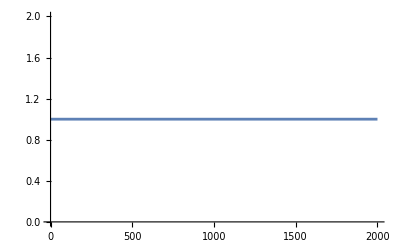

```mathematica
Plot[1-q,{r,0,2000}]
```

```mathematica
6L(FI[-P]FI[-Q]-1/3 FI[S]FI[-S]g3[-P,-Q])==  H[-P,-Q]
```

-(M (-2 M+r)^6)/r^9 | 0 | 0
0 | (M (-2 M+r)^6)/(2 r^9) | 0
0 | 0 | (M (-2 M+r)^6)/(2 r^9) |   |  
P | Q==-M/r^3 | 0 | 0
0 | M/(2 r^3) | 0
0 | 0 | M/(2 r^3) |   |  
P | Q

```mathematica
H[-P,-Q]
```

-M/r^3 | 0 | 0
0 | M/(2 r^3) | 0
0 | 0 | M/(2 r^3) |   |  
P | Q

```mathematica
cd[-b]@k[-a]+cd[-a]@k[-b]//Simplify
```

0

```mathematica
rho[r[],θ[]]->Sqrt[r[]^2+aa^2Cos[θ[]]^2]
```

ρ[r,θ]→√(a^2 Cos[θ]^2+r^2)

```mathematica
Conjugate[L]L//FullSimplify
```

((a^2 Cos[θ]^2+r^2)^5)/(M^2 (a^2+a^2 Cos[2 θ]+2 r (-2 M+r))^4)

```mathematica
L//Simplify
```

(ⅈ (a Cos[θ]-ⅈ r)^6)/(M (a Cos[θ]+ⅈ r) (a^2+a^2 Cos[2 θ]+2 r (-2 M+r))^2)

```mathematica
cd[-b]@k[-a]+cd[-a]@k[-b]//FullSimplify
```

0

```mathematica
fff=3/8(Alpha[P,-a,-b]Fd[a,b]ve[-P]Alpha[P,-a,-b]Fd[a,b]ve[-P]-4/3Fd[-a,-b]Fd[a,b])//FullSimplify
```

(8 M^2)/(ⅈ a Cos[θ]+r)^4

```mathematica
L=4ps2/fff//FullSimplify
```

-(ⅈ a Cos[θ]+r)/(2 M)

```mathematica
σE= 1-1+2mass/(r[]-I aa Cos[θ[]])
```

(2 M)/(-ⅈ a Cos[θ]+r)

```mathematica
-1/σE
```

-(-ⅈ a Cos[θ]+r)/(2 M)

```mathematica
Fd[-a,-b]Fd[a,b]//FullSimplify
```

-(4 M^2)/(ⅈ a Cos[θ]+r)^4

```mathematica
Alpha[P,-a,-b]Fd[a,b]ve[-P]Alpha[P,-a,-b]Fd[a,b]ve[-P]//FullSimplify
```

(16 M^2)/(ⅈ a Cos[θ]+r)^4